# Covid

## Analiza razlicnih aspektov epidemije v Sloveniji in po svetu

## Pridobivanje podatkov

Mathematica ima na voljo veliko podatkovno bazo Wolfram data repository.

```mathematica
ResourceSearch["COVID-19"]
```

ResourceObject::updav: There is an update available for resource "Epidemic Data for Novel Coronavirus COVID-19". Use ResourceUpdate[Epidemic Data for Novel Coronavirus COVID-19] to get the update.

ResourceObject::updav: There is an update available for resource "Genetic Sequences for the SARS-CoV-2 Coronavirus". Use ResourceUpdate[Genetic Sequences for the SARS-CoV-2 Coronavirus] to get the update.

General::stop: Further output of ResourceObject::updav will be suppressed during this calculation.

Posodobimo podatke:

```mathematica
ResourceUpdate["Epidemic Data for Novel Coronavirus COVID-19"];
```

Shranimo podatke:

```mathematica
podatki = ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];
```

```mathematica
podatki[[1;;10]](* prvih 10 vrstic podatkov *)
```

## Analiza primerov v Sloveniji

(Osnovni prikaz podatkov, par grafov)

```mathematica
Select[podatki, #["Country"] == LinguisticAssistant&]
```

```mathematica
potrjeniPrimeriSlovenija = %[[1]]["ConfirmedCases"]
```

TimeSeries[…]

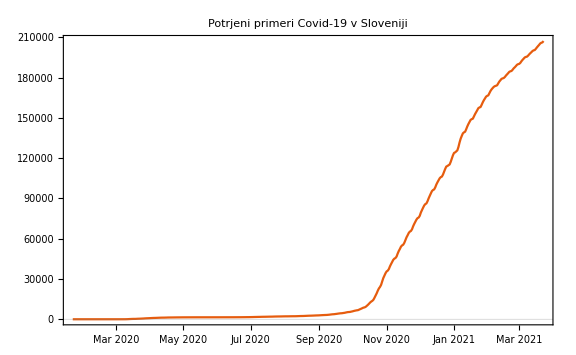

```mathematica
DateListPlot[potrjeniPrimeriSlovenija, PlotLabel->"Potrjeni primeri Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large]
```

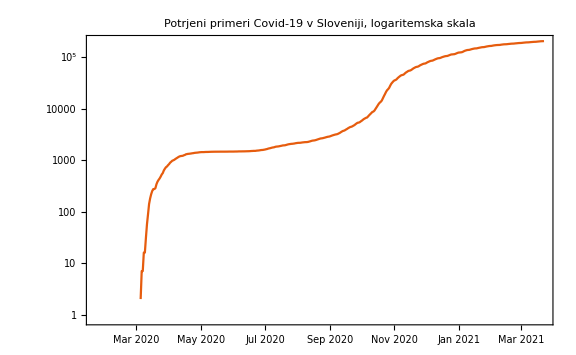

```mathematica
DateListLogPlot[potrjeniPrimeriSlovenija, PlotLabel->"Potrjeni primeri Covid-19 v Sloveniji, logaritemska skala", PlotTheme->"Scientific", ImageSize->Large]
```

Dnevno stevilo novih primerov:

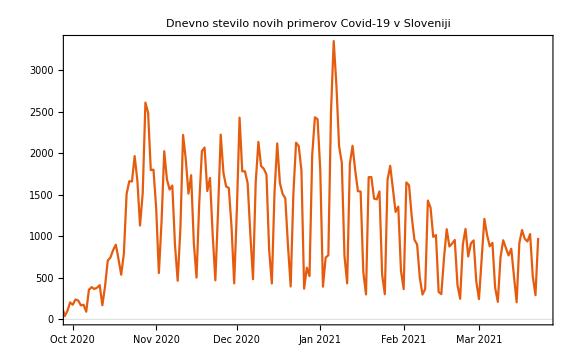

```mathematica
DateListPlot[Differences[potrjeniPrimeriSlovenija], PlotLabel->"Dnevno stevilo novih primerov Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large, PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic}]
```

Izracunamo 7-dnevno povprecje novih primerov v Sloveniji:

```mathematica
noviPrimeriSlovenija = MovingAverage[Differences[potrjeniPrimeriSlovenija], 7];
```

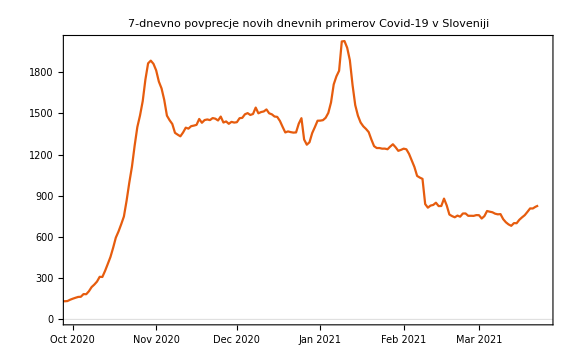

```mathematica
DateListPlot[noviPrimeriSlovenija, PlotLabel->"7-dnevno povprecje novih dnevnih primerov Covid-19 v Sloveniji", PlotTheme->"Scientific", ImageSize->Large,PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic} ]
```

Stevilo dnevnih novih primerov na 100.000 prebivalcev, 7-dnevno povprecje:

```mathematica
noviPrimeriNa100000Slovenija = 100000 * noviPrimeriSlovenija / LinguisticAssistant["Population"];
```

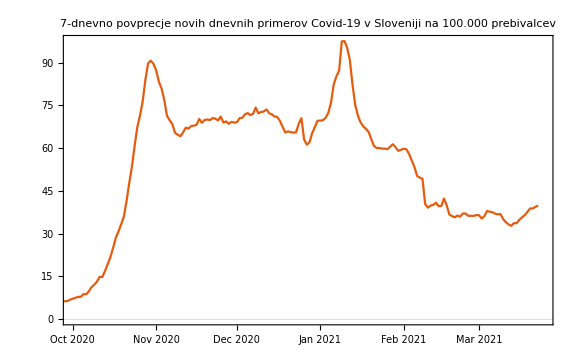

```mathematica
DateListPlot[noviPrimeriNa100000Slovenija, PlotLabel->"7-dnevno povprecje novih dnevnih primerov Covid-19 v Sloveniji na 100.000 prebivalcev", PlotTheme->"Scientific", ImageSize->Large,PlotRange->{{LinguisticAssistant,LinguisticAssistant},Automatic} ]
```